```mathematica
alfabet = Alphabet["Italian"];
alfabet2 = Tuples[alfabet,2];
aa =Table[StringJoin[{alfabet2[[t,1]],alfabet2[[t,2]]}],{t,1,Length[alfabet2]}];
slowa = Table[DictionaryLookup[{"Italian",aa[[t]]~~__}],{t,1,Length[aa]}];
ilosc= Table[Length[slowa[[t]]],{t,1,Length[slowa]}];
ilosclista = Partition[ilosc,Length[alfabet]];
```

```mathematica
dane = Table[{StringJoin[aa[[t]],".."],ilosc[[t]]},{t,1,Length[aa]}];
chmurka = WordCloud[dane,-Graphics-,ImageSize->790];
```

```mathematica
ticks= Table[{i,alfabet[[i]]},{i,1,Length[alfabet]}];
matrix = MatrixPlot[ilosclista,ColorFunction->"TemperatureMap",
FrameTicks->{ticks,ticks,ticks,ticks},
ImageSize->740,Mesh->All,ColorRules->{0->White},
Epilog->{Inset[GraphicsGrid[ilosclista,ImageSize->650],{Length[alfabet]/2,Length[alfabet]/2}]},
FrameLabel-> {"pierwsza litera","druga litera","pierwsza lietra","druga litera"}, 
PlotLegends->Placed[Framed["Liczba słów w języku włoskim"],Above]];
```

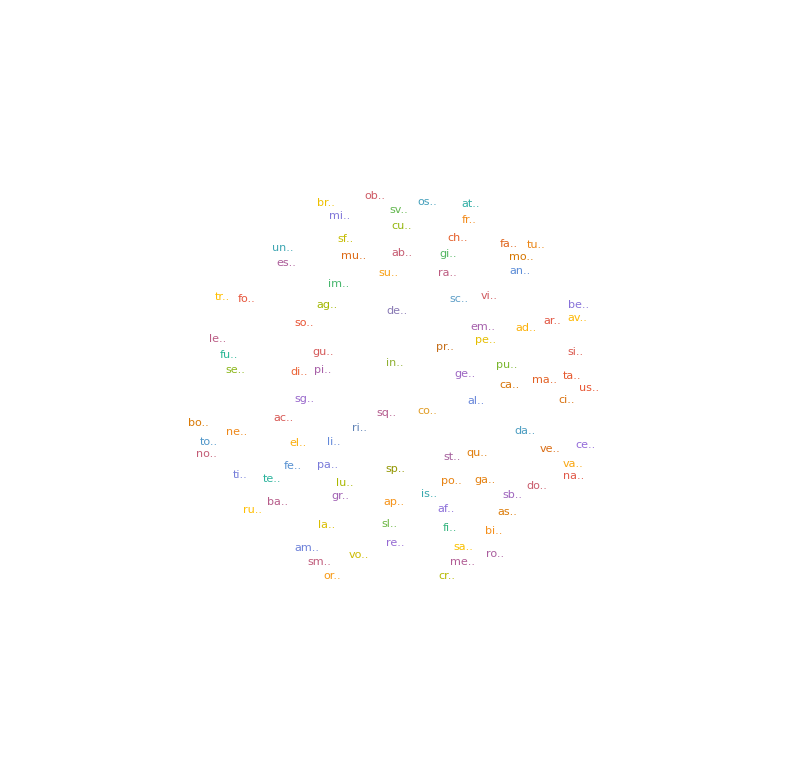

```mathematica
all = GraphicsGrid[{{matrix,chmurka}}]
```

```mathematica
CloudExport[all,"PDF"]
```

CloudObject[https://www.wolframcloud.com/obj/7c1bf4a2-6501-4c4b-bcf8-d6760543cd8d]